```mathematica
<<VisualDebug`
VisualDebug[2+2]
```

VisualDebug[2+2]

```mathematica
expr=Hold[{2+3,5^2,9+0}];
stringExpr=FullForm[expr]//ToString;
length=StringLength[stringExpr];
Manipulate[
startString=StringTake[stringExpr,{1,startPos-1}];
midString=StringTake[stringExpr,{startPos, endPos}];
endString=StringTake[stringExpr,{endPos+1,length}];
Row[{startString,Style[midString,FontColor->ColorData["Rainbow"][0.5]],endString}];
Row[{Style[Extract[expr,mainPart,HoldForm],FontColor->ColorData["Rainbow"][0.5]]}],

{startPos,1,endPos,1,Appearance->"Labeled"},
{{endPos,length},startPos, length,1,Appearance->"Labeled"},
{mainPart,0, Length[expr],1}
]
```

```mathematica
StringLength["Abc"]
```

3

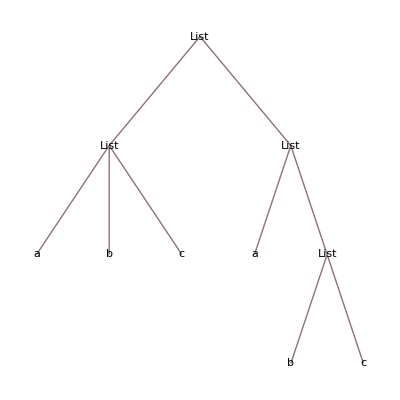

```mathematica
{{a,b,c},{a,{b,c}}}//TreeForm
```

```mathematica
a->0
{a}->1
{a,b}->{2,{0,0}}
shape@{{a,d},{b,c}}
```

a→0

{a}→1

{a,b}→{2,{0,0}}

shape[{{a,d},{b,c}}]

```mathematica
Depth[HoldForm[a]]
```

2

```mathematica
Remove[shape]
SetAttributes[shape,HoldAll]
shape[expr_]:=Module[
{

},
If[Depth[Unevaluated[expr]]==1,
Return[0],
Return[{Length[Unevaluated[expr]],shape@@@(Map[Unevaluated,ReplacePart[Hold[expr],{1,0}->List],{2}]//ReleaseHold)}]
]
]
```

```mathematica
expr1=Hold[2+2+Integrate[x^6+3,{x,0,2}]]
sh=shape[2+2+Integrate[x^6+3,{x,0,2}]]
Position[%,_List]
Extract[expr1,{1,3,1,1,2}]
```

Hold[2+2+∫_0^2 (x^6+3)ⅆx]

{3,{0,0,{2,{{2,{{2,{0,0}},0}},{3,{0,0,0}}}}}}

{{2,3,2,1,2,1,2},{2,3,2,1,2,1},{2,3,2,1,2},{2,3,2,1},{2,3,2,2,2},{2,3,2,2},{2,3,2},{2,3},{2},{}}

6

```mathematica
Extract[expr1,{1,3,1},Hold]
```

Hold[x^6+3]

```mathematica
Position[expr1,_]//Sort[#,Length[#1]<Length[#2]&]&
```

{{},{1},{0},{1,3},{1,2},{1,1},{1,0},{1,3,2},{1,3,1},{1,3,0},{1,3,2,3},{1,3,2,2},{1,3,2,1},{1,3,2,0},{1,3,1,2},{1,3,1,1},{1,3,1,0},{1,3,1,1,2},{1,3,1,1,1},{1,3,1,1,0}}

```mathematica
Position[expr1,_,Heads->False]//Sort//Rest
```

{{1},{1,1},{1,2},{1,3},{1,3,1},{1,3,2},{1,3,1,1},{1,3,1,2},{1,3,2,1},{1,3,2,2},{1,3,2,3},{1,3,1,1,1},{1,3,1,1,2}}

```mathematica
Position[expr1,_,Heads->True]//Sort//Rest
```

{{0},{1},{1,0},{1,1},{1,2},{1,3},{1,3,0},{1,3,1},{1,3,2},{1,3,1,0},{1,3,1,1},{1,3,1,2},{1,3,2,0},{1,3,2,1},{1,3,2,2},{1,3,2,3},{1,3,1,1,0},{1,3,1,1,1},{1,3,1,1,2}}

```mathematica
Remove[a]
```

```mathematica
a/:a+b=Exp
```

Exp

```mathematica
allowedParts=Position[expr1,_,Heads->False]//Sort//Rest
```

{{1},{1,1},{1,2},{1,3},{1,3,1},{1,3,2},{1,3,1,1},{1,3,1,2},{1,3,2,1},{1,3,2,2},{1,3,2,3},{1,3,1,1,1},{1,3,1,1,2}}

```mathematica
Remove[debug]
```

```mathematica
expr1=Hold[2+2+Integrate[x^6+3,{x,0,2}]];
SetAttributes[debug,HoldFirst]
debug[origExpr_,opts:OptionsPattern[{"Heads"->False}]]:=Module[
{
currentExpr,allowedParts,part
},
currentExpr=origExpr;
allowedParts=Position[currentExpr,_,Heads->OptionValue["Heads"]]//Sort//Rest;
Manipulate[
part=allowedParts[[partNumber]];
ReplacePart[currentExpr,part->Style[Extract[currentExpr,part,HoldForm],FontColor->RGBColor[1,0,0],Bold]],

{partNumber,If[OptionValue["Heads"],2,1],Dynamic[Length[allowedParts]],1},
Row[{
Button["Evaluate",
currentExpr=ReplacePart[currentExpr,part->Evaluate[Extract[currentExpr,part]]];
allowedParts=Position[currentExpr,_,Heads->OptionValue["Heads"]]//Sort//Rest
],
Button["Reset",
partNumber=If[OptionValue["Heads"],2,1];
currentExpr=origExpr;
allowedParts=Position[currentExpr,_,Heads->OptionValue["Heads"]]//Sort//Rest
]
}]
]
]
debug[expr1,Heads->False]
```

## From SE

```mathematica
SetAttributes[step,HoldAll]
step[expr_]:=Module[{P},P=(P= Return[#/.HoldForm[x_]:>Defer[step[x]],TraceScan]&)&;
TraceScan[P,expr,TraceDepth->1]]
```

```mathematica
expr1
step[2+2+∫_0^2 (x^6+3)ⅆx]
```

Hold[2+2+∫_0^2 (x^6+3)ⅆx]

step[2+2+170/7]

```mathematica
step[2+2+170/7]
```

step[2+2+170/7]

```mathematica
step[2+2+170/7]
```

step[2+2+170/7]

```mathematica
Hold[2+3^3^7]//FullForm
```

Hold[Plus[2,Power[3,Power[3,7]]]]